```mathematica
ClearAll["Global`*"];
deltaT = Symbol["ΔT"];
ClearAll[K, λ, m, α];
```

```mathematica
(*Effective Thermal Conductivity - A. Sellitto et al.*)

SellittoEffThermalCondKn  = λ*(1 - 2*Kn*((BesselJ[1, I /Kn]/BesselJ[0, I/ Kn])^2)*((BesselJ[0, I /Kn]/(I*BesselJ[1, I / Kn])) +  K))
```

λ (1-(2 Kn (K-(ⅈ BesselJ[0,ⅈ/Kn])/BesselJ[1,ⅈ/Kn]) BesselJ[1,ⅈ/Kn]^2)/BesselJ[0,ⅈ/Kn]^2)

```mathematica
(*Note that K is slip coefficient, Mathematica has prior associations with C*)

(*Effective thermal conductivity in terms of diameter(d)*)
SellittoEffThermalCond = SellittoEffThermalCondKn /. Kn -> l/R
```

λ (1-(2 l (K-(ⅈ BesselJ[0,(ⅈ R)/l])/BesselJ[1,(ⅈ R)/l]) BesselJ[1,(ⅈ R)/l]^2)/(R BesselJ[0,(ⅈ R)/l]^2))

```mathematica
(*Solving GK Equation with modification 'm' *)
(*Proper First Order Boundary Condition*)

modGKeqn = q''[r] + (1/r)*q'[r] - q[r]/((m^2)*l^2) == -λ*deltaT/(((m^2)*l^2)*L)
FirstOrderBC = {q'[0]==0,q[R]==-K*l*q'[R]};
FOsol = DSolve[{modGKeqn, FirstOrderBC}, q[r], r];

qFO = q[r] /. FOsol[[1]]
```

-q[r]/(l^2 m^2)+q'[r]/r+q''[r]==-(ΔT λ)/(l^2 L m^2)

-(ΔT λ (m BesselJ[0,(ⅈ r)/(l m)]-m BesselJ[0,(ⅈ R)/(l m)]+ⅈ K BesselJ[1,(ⅈ R)/(l m)]))/(L (m BesselJ[0,(ⅈ R)/(l m)]-ⅈ K BesselJ[1,(ⅈ R)/(l m)]))

```mathematica
FOrderEffThermalCond = Integrate[qFO*2*π*r, {r, 0, R}]/(π*(R^2)*(deltaT/L))
FOrderEffThermalCondKn = FOrderEffThermalCond /. R -> l/Kn // Simplify
```

(L λ (m R BesselI[0,R/(l m)]+(-2 l m^2+K R) BesselI[1,R/(l m)]))/(R (L m BesselI[0,R/(l m)]+K L BesselI[1,R/(l m)]))

(λ (m BesselI[0,1/(Kn m)]+(K-2 Kn m^2) BesselI[1,1/(Kn m)]))/(m BesselI[0,1/(Kn m)]+K BesselI[1,1/(Kn m)])

```mathematica
(*Second Order Boundary Condition*)

modGKeqn = q''[r] + (1/r)*q'[r] - q[r]/((m^2)*l^2) == -λ*deltaT/(((m^2)*l^2)*L)
SecondOrderBC = {q'[0]==0,q[R]==-K*l*q'[R] + α*l*l*q''[R]};
SOsol = DSolve[{modGKeqn, SecondOrderBC}, q[r], r];

qSO = q[r] /. SOsol[[1]] // Simplify
```

-q[r]/(l^2 m^2)+q'[r]/r+q''[r]==-(ΔT λ)/(l^2 L m^2)

-(ΔT λ (m^2 R BesselJ[0,(ⅈ r)/(l m)]+R (-m^2+α) BesselJ[0,(ⅈ R)/(l m)]+ⅈ m (K R+l α) BesselJ[1,(ⅈ R)/(l m)]))/(L (R (m^2-α) BesselJ[0,(ⅈ R)/(l m)]-ⅈ m (K R+l α) BesselJ[1,(ⅈ R)/(l m)]))

```mathematica
SOrderEffThermalCond = Integrate[qSO*2*π*r, {r, 0, R}]/(π*(R^2)*(deltaT/L)) // Simplify
SOrderEffThermalCondKn = SOrderEffThermalCond /. R -> l/Kn // Simplify
```

(λ (R (m^2-α) BesselI[0,R/(l m)]+m (K R+l (-2 m^2+α)) BesselI[1,R/(l m)]))/(R (m^2-α) BesselI[0,R/(l m)]+m (K R+l α) BesselI[1,R/(l m)])

(λ ((m^2-α) BesselI[0,1/(Kn m)]+m (K+Kn (-2 m^2+α)) BesselI[1,1/(Kn m)]))/((m^2-α) BesselI[0,1/(Kn m)]+m (K+Kn α) BesselI[1,1/(Kn m)])

General::munfl: 1/(0.+4.71020785901165×10^2123 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

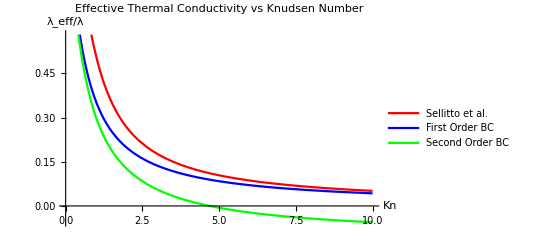

```mathematica
(*Effective Thermal Conductivity vs Knudsen Number*)

λ = 1;
K = 1;
m = Sqrt[18/(5*3.1415)];
α = 2/9;

Plot[{SellittoEffThermalCondKn, FOrderEffThermalCondKn, SOrderEffThermalCondKn}, {Kn, 0, 10}, PlotStyle -> {Red, Blue, Green}, PlotLegends -> {"Sellitto et al.", "First Order BC", "Second Order BC"}, AxesLabel->{"Kn", "λ_eff/λ"}, PlotLabel -> "Effective Thermal Conductivity vs Knudsen Number"]
```

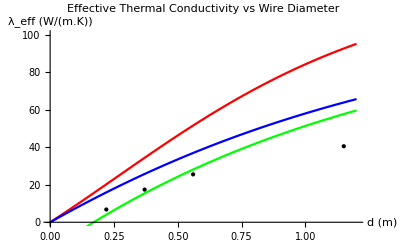

```mathematica
(*Effective Thermal Conductivity vs Radius of nanowire*)

ClearAll[K, λ, m, α];
PltSellitto = SellittoEffThermalCond /. R -> d/2;
PltFO = FOrderEffThermalCond /. R-> d/2;
PltSO = SOrderEffThermalCond /. R->d/2;

λ = 140; (*Silicon at 300K*)
l = 40*(10)^(-9); (*Silicon at 300K*)
K = 1;
m = Sqrt[18/(5*Pi)];
α = 2/9;

LiPoints={{22*10^(-9), 6.8}, {37*10^(-9),17.4},{56*10^(-9),25.5},{115*10^(-9),40.5}};

pointsPlot=Legended[ListPlot[LiPoints,PlotStyle->{Black,PointSize[Large]}],"Li et al."];
SellittoPlot=Legended[Plot[PltSellitto,{d,0,120*(10)^(-9)},PlotStyle->Red],"Sellitto et al."];
FOPlot=Legended[Plot[PltFO,{d,0,120*(10)^(-9)},PlotStyle->Blue],"First Order BC"];
SOPlot=Legended[Plot[PltSO,{d,0,120*(10)^(-9)},PlotStyle->Green],"Second Order BC"];

Show[SellittoPlot, FOPlot, SOPlot, pointsPlot,PlotLabel->"Effective Thermal Conductivity vs Wire Diameter",AxesLabel->{"d (m)","λ_eff (W/(m.K))"}, PlotRange -> {{0, 120*10^(-9)}, {0, 100}}, AxesOrigin -> {0,0}]
```

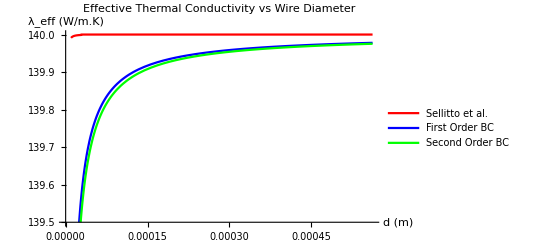

```mathematica
(*Validation at Macroscale Limit*)
Plot[{PltSellitto, PltFO, PltSO},{d,10*10^(-6),562*(10)^(-6)},PlotLegends->{"Sellitto et al.",  "First Order BC", "Second Order BC"},PlotStyle->{Red, Blue, Green},AxesLabel->{"d (m)","λ_eff (W/m.K)"},PlotLabel->"Effective Thermal Conductivity vs Wire Diameter", PlotRange->{{10^(-7), 562*10^(-6)}, {139.5, 140}}, AxesOrigin -> {10^(-7), 139.5}]

(*Note the Plot limits*)
```

```mathematica
(* 90% of Bulk Value*)

FindRoot[PltFO == 138.6,{d,2*10^(-7)}] (*Diameter at which 90% of saturation value is reached by SO BC solution*)
FindRoot[PltSellitto == 138.6,{d,2*10^(-7)}](*Diameter at which 90% of saturation value is reached by Sellitto et al.*)
```

{d→8.83299×10^-6}

{d→7.89876×10^-7+0. ⅈ}

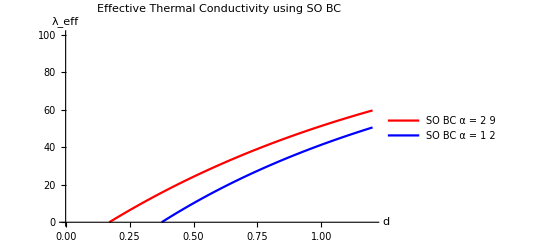

{d→1.7047×10^-8}

{d→3.75376×10^-8}

```mathematica
(*Critical Radius Calculations*)

ClearAll[K, λ, m, α];
AltPltSO = PltSO /. α -> α1;

λ = 140; (*Silicon at 300K*)
l = 40*(10)^(-9); (*Silicon at 300K*)
K = 1;
m = Sqrt[18/(5*Pi)];
α = 2/9;
α1 = 1/2;

Plot[{PltSO, AltPltSO},{d,0,120*10^(-9)},PlotLegends->{"SO BC α = 2
9",  "SO BC α = 1
2"},PlotStyle->{Red, Blue},AxesLabel->{"d","λ_eff"},PlotLabel->"Effective Thermal Conductivity using SO BC", PlotRange->{{0,120*10^(-9)},{0, 100}}, AxesOrigin -> {0,0}]
FindRoot[PltSO == 0,{d,2*10^(-9)}] (*Critical diameter at α = 2/9*)
FindRoot[AltPltSO == 0,{d,2*10^(-9)}] (*Critical diameter at α = 1/2*)
```

```mathematica
(*Discrepancy Evaluation in Sellitto et al.*)
(*First Order Additive Boundary Condition*)

deltaT = Symbol["ΔT"];
ClearAll[K, λ, m, α, l];

GKeqn = q''[r] + (1/r)*q'[r] - q[r]/(l^2) == -λ*deltaT/((l^2)*L)
AdditiveBC = {q'[0]==0,q[R]==0};
BulkSol = DSolve[{GKeqn, AdditiveBC}, q[r], r];

qBulk = q[r] /.BulkSol[[1]]
firstOrderSlip = q'[r]/. D[BulkSol[[1]], r] /. r-> R;
qWall = -K*l*firstOrderSlip

qTotal = qBulk + qWall // Simplify
```

-q[r]/l^2+q'[r]/r+q''[r]==-(ΔT λ)/(l^2 L)

-(ΔT λ (BesselJ[0,(ⅈ r)/l]-BesselJ[0,(ⅈ R)/l]))/(L BesselJ[0,(ⅈ R)/l])

-(ⅈ K ΔT λ BesselJ[1,(ⅈ R)/l])/(L BesselJ[0,(ⅈ R)/l])

(ΔT λ (-BesselJ[0,(ⅈ r)/l]+BesselJ[0,(ⅈ R)/l]-ⅈ K BesselJ[1,(ⅈ R)/l]))/(L BesselJ[0,(ⅈ R)/l])

```mathematica
AdditiveFOThermalCond = Integrate[qTotal*2*π*r, {r, 0, R}]/(π*(R^2)*(deltaT/L));
AdditiveFOThermalCondKn =  AdditiveFOThermalCond /. R -> l/Kn  // Simplify
AdditiveFOThermalCond = AdditiveFOThermalCond /. R -> d/2 // Simplify
```

λ+((K-2 Kn) λ BesselI[1,1/Kn])/BesselI[0,1/Kn]

λ+((d K-4 l) λ BesselI[1,d/(2 l)])/(d BesselI[0,d/(2 l)])

```mathematica
λ = 140; (*Silicon at 300K*)
l = 40*(10)^(-9); (*Silicon at 300K*)
K = 1;
```

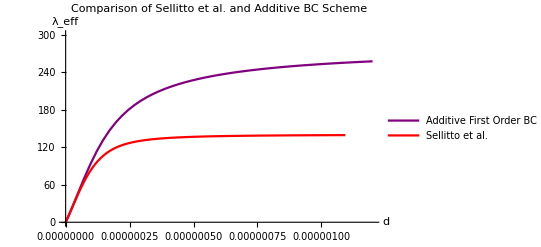

```mathematica
Plot[{AdditiveFOThermalCond, PltSellitto},{d,0*10^(-8),120*10^(-8)},PlotLegends->{"Additive First Order BC",  "Sellitto et al."},PlotStyle->{Purple, Red},AxesLabel->{"d","λ_eff"},PlotLabel->"Comparison of Sellitto et al. and Additive BC Scheme", PlotRange->{{0,120*10^(-8)},{0, 300}}]
```